numerov with  cosine potential

```mathematica
(*Potential*)
V[s_]:=10*Cos[s];
(*fix size of hamiltonian at 500 x 500, and sample s ∈(-π/500,2π-π/500) uniformly*)
n=500;d=2.π/n;
s=Table[-d/2.+d i,{i,n}];
(*calculate KE matrix, impose periodic boundary conditions by coupling ψ[n] and ψ[1] with each other*)
𝕀[n_,d_]:=DiagonalMatrix[1+0Range[n-Abs[d]],d];
B=1./12(𝕀[n,-1]+10 𝕀[n,0]+𝕀[n,1]+𝕀[n,n-1]+𝕀[n,-n+1]);
A=1/d^2(𝕀[n,-1]-2 𝕀[n,0]+𝕀[n,1]+𝕀[n,n-1]+𝕀[n,-n+1]);
KE=-1/2 Inverse[B].A;
(*Hamiltonian*)
H=KE+DiagonalMatrix[V[s]];
(*Energies, wavefunctions*)
{eval,evec}=Eigensystem[H];
```

```mathematica
numerov[j_]:=Table[{s[[i]],(evec[[j]][[i]])/d^0.5},{i,1,n}]
```

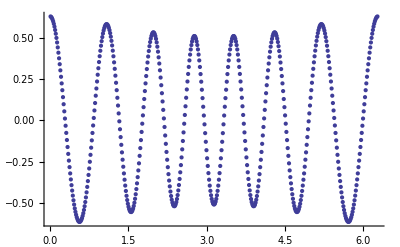

```mathematica
ListPlot[numerov[-15]]
```

Theoretical Eigenvalues

```mathematica
v=10;
```

```mathematica
eths=Sort[Table[8^-1*MathieuCharacteristicB[r,4*v]//N,{r,1,50}],Abs[#1]<Abs[#2]&];
```

```mathematica
ethc=Sort[Table[8^-1*MathieuCharacteristicA[r,4*v]//N,{r,1,50}],Abs[#1]<Abs[#2]&];
```

```mathematica
(*Theory Eigenvalues*)
```

```mathematica
eth=Sort[Join[eths,ethc],Abs[#1]<Abs[#2]&];
```

```mathematica
eth[[;;20]]
```

{0.216206,0.216256,-2.52599,-2.52599,2.79066,2.79152,5.16872,5.17913,-5.41903,-5.41903,7.27889,7.3653,-8.45077,8.95526,9.38939,10.229,11.392,11.6457,13.5558,13.5992}

```mathematica
(*Numerov Eigenvalues*)
```

```mathematica
evals=Sort[eval,Abs[#1]<Abs[#2]&];
```

```mathematica
evals[[;;20]]
```

{0.216256,-2.52599,2.79066,5.17913,-5.41903,7.27888,-8.45077,9.38939,10.229,13.5558,13.5992,18.7184,18.7189,25.02,25.02,32.3953,32.3953,40.8111,40.8111,50.2514}